```mathematica
Remove["Global`*"]
```

```mathematica
Needs["Units`"]
```

fϕOuter[r_]  = ((Q2 Sinh[κ*R2]/(4*π*ϵ*κ*))

```mathematica
$MinPrecision=100
 


ϕWithinShells[r_]  = (((Q2*Exp[-κ*R2]) /(4 Pi*ϵ*κ*R2) ) - ((Q1*Exp[-κ*R1]) /(4 Pi*ϵ*κ*R1) )) * (Sinh[κ*r]/r)
ϕBetweenShells[r_] = (((Q2*Exp[-κ*R2]) /(4 Pi*ϵ*κ*R2) )+((Q1*Sinh[κ*R1] /(4 *Pi*ϵ*κ*R1) ))) *(Sinh[κ*r]/r)   -   ((Q1*Sinh[κ*R1] /(4 *Pi*ϵ*κ*R1) )*(Cosh[κ*r]/r))
ϕOutsideShells[r_] = ((Q2*Sinh[κ*R2]/((4 Pi*ϵ*κ*R2)))-((Q1*Sinh[κ*R1])/(4 Pi*ϵ*κ*R1))) * (Exp[-κ*r]/r)
```

100

((-(ⅇ^(-R1 κ) Q1)/(4 π R1 ϵ κ)+(ⅇ^(-R2 κ) Q2)/(4 π R2 ϵ κ)) Sinh[r κ])/r

-(Q1 Cosh[r κ] Sinh[R1 κ])/(4 π r R1 ϵ κ)+(Sinh[r κ] ((ⅇ^(-R2 κ) Q2)/(4 π R2 ϵ κ)+(Q1 Sinh[R1 κ])/(4 π R1 ϵ κ)))/r

(ⅇ^(-r κ) (-(Q1 Sinh[R1 κ])/(4 π R1 ϵ κ)+(Q2 Sinh[R2 κ])/(4 π R2 ϵ κ)))/r

```mathematica
ϕShells[r_] = Piecewise[{{ϕWithinShells[r] ,r≤R1},{ϕBetweenShells[r] ,R1<r≤R2},{ϕOutsideShells[r],r>R2}}]
compensatingCharge[r_] = (-(κ^2) * ϕShells[r])
```

Piecewise[{{((-(ⅇ^(-R1 κ) Q1)/(4 π R1 ϵ κ)+(ⅇ^(-R2 κ) Q2)/(4 π R2 ϵ κ)) Sinh[r κ])/r, r≤R1}, {-(Q1 Cosh[r κ] Sinh[R1 κ])/(4 π r R1 ϵ κ)+(Sinh[r κ] ((ⅇ^(-R2 κ) Q2)/(4 π R2 ϵ κ)+(Q1 Sinh[R1 κ])/(4 π R1 ϵ κ)))/r, R1<r≤R2}, {(ⅇ^(-r κ) (-(Q1 Sinh[R1 κ])/(4 π R1 ϵ κ)+(Q2 Sinh[R2 κ])/(4 π R2 ϵ κ)))/r, r>R2}, {0, True}}]

-κ^2 (Piecewise[{{((-(ⅇ^(-R1 κ) Q1)/(4 π R1 ϵ κ)+(ⅇ^(-R2 κ) Q2)/(4 π R2 ϵ κ)) Sinh[r κ])/r, r≤R1}, {-(Q1 Cosh[r κ] Sinh[R1 κ])/(4 π r R1 ϵ κ)+(Sinh[r κ] ((ⅇ^(-R2 κ) Q2)/(4 π R2 ϵ κ)+(Q1 Sinh[R1 κ])/(4 π R1 ϵ κ)))/r, R1<r≤R2}, {(ⅇ^(-r κ) (-(Q1 Sinh[R1 κ])/(4 π R1 ϵ κ)+(Q2 Sinh[R2 κ])/(4 π R2 ϵ κ)))/r, r>R2}, {0, True}}])

linearized Debye-H¨uckel approximation

```mathematica
Efield[r_] = D[ϕShells[r],r]
```

Piecewise[{{((-(ⅇ^(-R1 κ) Q1)/(4 π R1 ϵ κ)+(ⅇ^(-R2 κ) Q2)/(4 π R2 ϵ κ)) κ Cosh[r κ])/r-((-(ⅇ^(-R1 κ) Q1)/(4 π R1 ϵ κ)+(ⅇ^(-R2 κ) Q2)/(4 π R2 ϵ κ)) Sinh[r κ])/r^2, r-R1≤0}, {(Q1 Cosh[r κ] Sinh[R1 κ])/(4 π r^2 R1 ϵ κ)-(Q1 Sinh[r κ] Sinh[R1 κ])/(4 π r R1 ϵ)+(κ Cosh[r κ] ((ⅇ^(-R2 κ) Q2)/(4 π R2 ϵ κ)+(Q1 Sinh[R1 κ])/(4 π R1 ϵ κ)))/r-(Sinh[r κ] ((ⅇ^(-R2 κ) Q2)/(4 π R2 ϵ κ)+(Q1 Sinh[R1 κ])/(4 π R1 ϵ κ)))/r^2, r-R1>0&&r-R2≤0}, {-(ⅇ^(-r κ) (-(Q1 Sinh[R1 κ])/(4 π R1 ϵ κ)+(Q2 Sinh[R2 κ])/(4 π R2 ϵ κ)))/r^2-(ⅇ^(-r κ) κ (-(Q1 Sinh[R1 κ])/(4 π R1 ϵ κ)+(Q2 Sinh[R2 κ])/(4 π R2 ϵ κ)))/r, r-R2>0}, {0, True}}]

```mathematica
IncidentField = 1*^6
```

1000000

κ = Sqrt[(2*((e0)^2)/(ϵ*kB*310))*0.1]

```mathematica
scale =1*10^-9
R1 = SetPrecision[40*10^-9,100] 
el =10*^-9 
R2 =SetPrecision[100*10^-9,100]
e0 =SetPrecision[1.602*^-19,100]
Q1 =SetPrecision[10000.0*e0,100]
Q2 =SetPrecision[-10000.0*e0,100]
kB = 1.38*^-23
κ = SetPrecision[(1/(5*^-9)),100]

ϵ0 =SetPrecision[ 8.85*^-12,100]
ϵ = SetPrecision[80.0*ϵ0,100]
```

1/1000000000

4.×10^-8

1/100000000

1.×10^-7

1.601999999999999978640309261765471836909903261751174168535383213196610086015425622463226318359375×10^-19

1.60199999999999999905516667227017187930326945315140374503926068427972495555877685546875×10^-15

-1.60199999999999999905516667227017187930326945315140374503926068427972495555877685546875×10^-15

1.38×10^-23

2.×10^8

8.8500000000000004581342654891361158842055800732850912027060985565185546875×10^-12

7.08000000000000036650741239130889270736446405862807296216487884521484375×10^-10

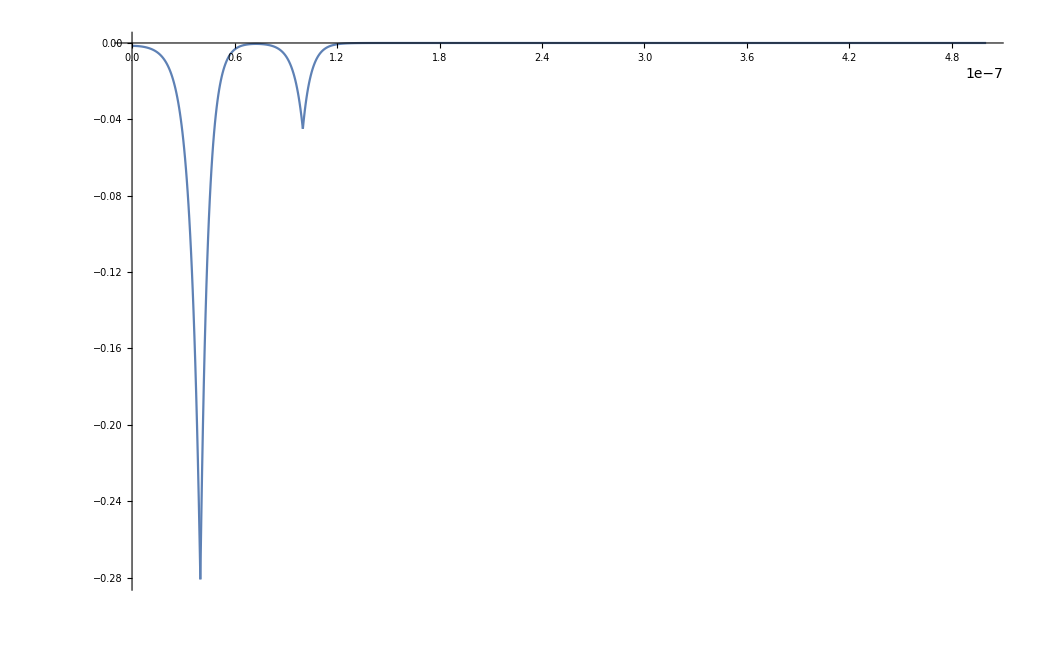

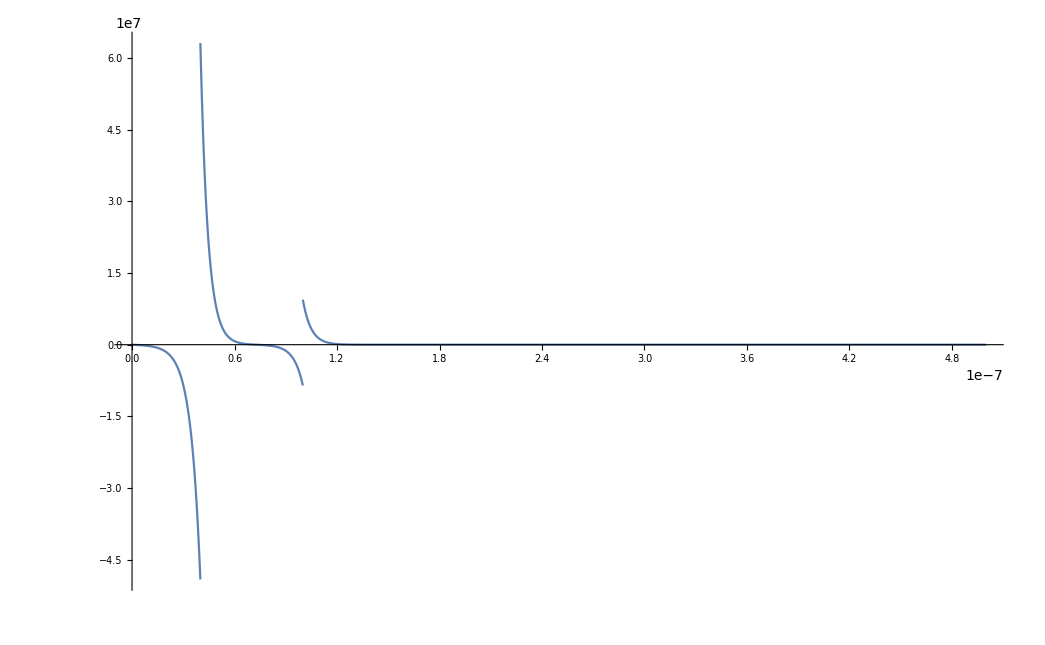

-Graphics-

```mathematica
Plot[ϕShells[x],{x,0,R2*5},PlotRange->All, PlotPoints->1000]
Plot[Efield[x],{x,0,R2*5},PlotRange->All, PlotPoints->1000]
Plot[compensatingCharge[x],{x,0,R2*5},PlotRange->All, PlotPoints->1000]
```

Note that this is not physical; first, because it assumes the dielectric and kappas are identical between the inside and outside of the virus, but also an unphysical debye length of 5 nm (rather than 1 nm for physiological) was required because of numerical discretization, and
A much more detailed finite-element treatment will be required to determine the magnitude of the effect.

that charge density implies a charge of 2*10^9 * (50*10^-9)^3 / 1.602*^-19 = 10^6
HUH
does that account for the large charge seen by Yang et al?
100 nm ^3 = 10^-18 L, which can have 10^8 atoms in it
that's still pretty remarkable

```mathematica
len = 1.5
Plot3D[ϕShells[Sqrt[x^2+y^2]],{x,-len*R2,R2*len},{y,-len*R2,R2*len}, PlotRange->All] 
Plot3D[Efield[Sqrt[x^2+y^2]],{x,-len*R2,R2*len},{y,-len*R2,R2*len}, PlotRange->All]
Plot3D[compensatingCharge[Sqrt[x^2+y^2]],{x,-len*R2,R2*len},{y,-len*R2,R2*len}, PlotRange->All]
```

1.5

-Graphics3D-

-Graphics3D-

-Graphics3D-